# Fisher estimates for a power law mass spectrum

```mathematica
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

## No selection effects

## Inputs

```mathematica
$Assumptions={θ>0,θmax>0,θmin>0,θmax>θmin, σ>0 & σ<1000,λ>-1}
```

{θ>0,θmax>0,θmin>0,θmax>θmin,σ (σ>0&)<1000,λ>-1}

In this first example we do not consider selection effects, meaning we set the probability of detection for both source and population parameters to one.

```mathematica
pdetθ[M_]:=1
pdetλ[λ_]:=1
ppop[{θ_,θmin_,θmax_},λ_]:= λ/(θmax^λ-θmin^λ) θ^(λ-1)
```

We check here that the population model is correctly normalized.

```mathematica
Integrate[ppop[{θ,θmin,θmax},λ],{θ,θmin,θmax}]
```

1

A bunch of useful quantities that enter the Fisher matrix.

```mathematica
Γ = 1/σ^2;  (* True only in the case in which d = θ + noise. *)
Dmij= Γ ;  (* Only true in the absence of selection effects. *)
Dmi = D[pdetθ[θ],θ];
P = D[Log@ppop[{θ,θmin,θmax},λ],θ];
H = - D[D[Log@ppop[{θ,θmin,θmax},λ],θ],θ];
```

Choose the true parameters here.

```mathematica
λtrue =0.00001;
truepars ={Nobs->1000,λ->λtrue,σ->0.1,θmax->10^7, θmin->10^4}//N;
```

## Fisher matrix and precision estimates [only retaining first term]

In this simplified scenario, we only consider the first (dominant) contribution to the Fisher matrix, without considering selection effects.
Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
SimpPopFisherNoSelectionEffects[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=
Integrate[(1/ppop[{θ,θmin,θmax},λ])D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,θmin,θmax}]
```

```mathematica
ΓλλSimpNoSelectionEffects = SimpPopFisherNoSelectionEffects[λ,{M,Mmin,Mmax},{λ,λ}];//Timing
```

{226.683,Null}

```mathematica
√(1/(Nobs*ΓλλSimpNoSelectionEffects))
Δα =%/.{Mmax->θmax, Mmin->θmin}/.truepars
```

√(1/(Nobs (1/λ^2-(Mmax^λ Mmin^λ (Log[Mmax]-Log[Mmin])^2)/((Mmax^λ-Mmin^λ)^2))))

0.0157423

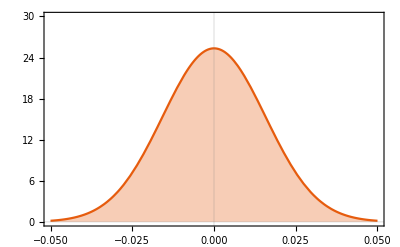

```mathematica
SimplifiedFisher=Plot[
PDF[NormalDistribution[λtrue,Δα],x]//Evaluate,{x,-.05,.05},
Filling->Axis,PlotRange->{All,{0,30}},
FrameLabel->{{MaTeX["\\text{PDF}",FontSize->17],None},{MaTeX["\\alpha_0",FontSize->17],None}},
FrameTicksStyle->Directive[Black,13],
TicksStyle->Directive[Black,AbsoluteThickness[100]],
PlotTheme-> "Scientific", 
Frame->True]
```

## Fisher matrix and precision estimates [including all terms]

Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
Γλλ=With[{θmin =10^4 ,θmax = 10^7,Γ = Γ, H = H, D2 = Dmij,D1=Dmi},
model = ppop[{θ,θmin,θmax},λ];
a = Integrate[(pdetθ[θ]/(model pdetλ[λ]))D[model,λ]*D[model,λ],{θ,θmin,θmax}];
b = - 1/pdetλ[λ]^2 D[pdetλ[λ],λ]*D[pdetλ[λ],λ];
c = 1/2 Integrate[D[D[Log@(Γ+H),λ],λ] pdetθ[θ]/pdetλ[λ] model,{θ,θmin,θmax}];
d =-1/2 Integrate[D[D[(Γ+H)^-1,λ],λ]D2 model/pdetλ[λ],{θ,θmin,θmax}];
e =- Integrate[D[D[P(Γ+H)^-1,λ],λ]D1 model/pdetλ[λ],{θ,θmin,θmax}];
f = -Integrate[D[D[P^2(Γ+H)^-1,λ],λ] model/pdetλ[λ],{θ,θmin,θmax}];
a+b+c+d+e+f
];//Timing
```

{62.2145,Null}

```mathematica
√(1/(Nobs*Γλλ));
%/.truepars
Δαfull=Re[%]
```

0.0158814+8.87709×10^-10 ⅈ

0.0158814

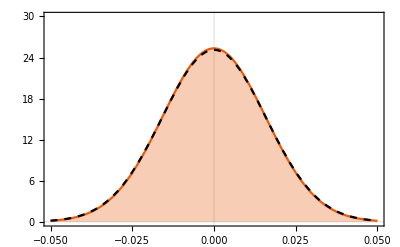

```mathematica
FullFisher = Plot[PDF[NormalDistribution[λtrue,Δαfull],x]//Evaluate,{x,-.05,.05},PlotStyle->{Black,Dashed}];
Show[SimplifiedFisher,FullFisher]
```

## With selection effects

The aim here is not to calculate the expression analytically, as it would be too hard to do. 
We instead help the numerical integration in Python by obtaining some analytical expressions that are valid for the specific case of a power law distribution.

```mathematica
$Assumptions={σ>0};
```

```mathematica
σθ=1/2 Erfc[(dth-θ)/(√2 √(σ^2))]; 
pθλ = ppop[{θ,θmin,θmax},λ];
```

```mathematica
Dm1 = D[σθ,θ];
Dm2 = Γ;
Hij=-D[D[pθλ,θ],θ];
```

```mathematica
somepars={θmin->10^4,θmax->10^7};
```

The FM expression can be written as int of function of θ times p(θ|λ), integrated over θ, which can be treated with Monte Carlo methods by drawing samples from p(θ|λ) and using them as input for the function of θ. Below are the expressions needed for such a function of θ.

```mathematica
aa =-pθ/pλ D[D[Log[pθλ/σλ[λ]],λ],λ]//Simplify;
```

```mathematica
bb=1/2 pθ/pλ D[D[Log[Γ+Hij],λ],λ]//Simplify;
```

```mathematica
cc =-1/2 Dm2/pλ D[D[Log[(Γ+Hij)^-1],λ],λ]//Simplify;
```

```mathematica
dd = -Dm1/pλ D[D[Log[P(Γ+Hij)^-1],λ],λ]//Simplify;
```

```mathematica
ee = -1/2 pθ/pλ D[D[Log[P^2(Γ+Hij)^-1],λ],λ]//Simplify;
```

```mathematica
Fofθ = aa+bb+cc+dd+ee//Simplify;//Timing
```

{4.10649,Null}

```mathematica
Fofθ//.σλ->Function[{λ},1.0]//.{θmax->10^7,θmin->10^4,λ->0.00001,σ->0.1,dth->13.012,θ->Exp[12.62]}//N//Simplify
```

General::munfl: Exp[-4.57641×10^12] is too small to represent as a normalized machine number; precision may be lost.

(1.5161×10^-17+5.0352 pθ)/pλ

```mathematica
Fofθ//.{θmax->10^7,θmin->10^4,λ->0.00001,σ->0.1,dth->13.012}//N//FullSimplify
```

1/pλ 0.5 ((pθ (0.00475506+99.6707 θ^2.99999-345.444 θ^5.99998+(9.71562×10^-14+θ^2.99999 (-14.1643+0.5 Log[θ])-5.57037×10^-19 Log[θ]) Log[θ]))/(-0.00144744+1. θ^2.99999-172.718 θ^5.99998)+(θ^2.99999 (-0.00442918-5.62395×10^-14 Log[θ])+θ^5.99998 (-56.5491+(8.20079-0.289489 Log[θ]) Log[θ]))/(8.38037×10^-6 θ^2.99999-0.00578977 θ^5.99998+1. θ^8.99997)+(pθ (-0.0000442918-5.62395×10^-16 Log[θ]+θ^2.99999 (-0.565491+(0.0820079-0.00289489 Log[θ]) Log[θ])))/((0.00289489-1. θ^2.99999)^2)+2. pθ (4.03518+(-1. σλ'[0.00001]^2+σλ[0.00001] σλ''[0.00001])/σλ[0.00001]^2))

```mathematica
(* This is what is coded up in the Python notebook. *)
```

```mathematica
D[pθλ,λ]/.{θ->Exp[θ]}//Simplify
D[D[pθλ,λ],λ]/.{θ->Exp[θ]}//FullSimplify
```

((ⅇ^θ)^(-1+λ) (θmax^λ-θmin^λ+(θmax^λ-θmin^λ) λ Log[ⅇ^θ]-θmax^λ λ Log[θmax]+θmin^λ λ Log[θmin]))/((θmax^λ-θmin^λ)^2)

1/((θmax^λ-θmin^λ)^3)(ⅇ^θ)^(-1+λ) (θmax^(2 λ) (Log[ⅇ^θ]-Log[θmax]) (2+λ Log[ⅇ^θ]-λ Log[θmax])+θmin^(2 λ) (Log[ⅇ^θ]-Log[θmin]) (2+λ Log[ⅇ^θ]-λ Log[θmin])+θmax^λ θmin^λ (-2 λ Log[ⅇ^θ]^2+2 (Log[θmax]+Log[θmin])+λ (Log[θmax]^2-4 Log[θmax] Log[θmin]+Log[θmin]^2)+2 Log[ⅇ^θ] (-2+λ (Log[θmax]+Log[θmin]))))

```mathematica
-D[D[Log[model[λ]/pλ[λ]],λ],λ]//FullSimplify
```

(model'[λ]^2-model[λ] model''[λ])/model[λ]^2+(-pλ'[λ]^2+pλ[λ] pλ''[λ])/pλ[λ]^2